Network Graph Theory

```mathematica
myKonigsbergMatrix:= {1->2,2->1,2->3,3->1,3->4,4->1,1->4}
Graph[myKonigsbergMatrix, VertexLabels->"Name", ImagePadding->10]
```

-Graphics-

```mathematica
myFriendsMatrix:= {1->2,1->3,2->3,2->4,4->1,4->3,2->5,1->5,3->5}
Graph[myFriendsMatrix, VertexLabels->"Name", ImagePadding->10]
```

-Graphics-

```mathematica
myMatrix1:=({{0, 1, 1, 1}, {1, 0, 0, 0}, {1, 0, 0, 0}, {1, 0, 0, 0}})
```

```mathematica
AdjacencyGraph[myMatrix1,DirectedEdges->False,EdgeStyle->Arrowheads[Medium],EdgeShapeFunction->"Arrow", VertexLabels->"Name",ImagePadding->10 ]
```

-Graphics-

```mathematica
myMatrix2:=({{0, 0, 1, 1}, {0, 0, 1, 1}, {1, 1, 0, 0}, {1, 1, 0, 0}})
```

```mathematica
AdjacencyGraph[myMatrix2,DirectedEdges->False,EdgeStyle->Arrowheads[Medium],EdgeShapeFunction->"Arrow", VertexLabels->"Name",ImagePadding->10 ]
```

-Graphics-

```mathematica
myMatrix3:=({{0, 0, 1, 1}, {0, 0, 1, 1}, {1, 1, 0, 1}, {1, 1, 1, 0}})
```

```mathematica
AdjacencyGraph[myMatrix3,DirectedEdges->False,EdgeStyle->Arrowheads[Medium],EdgeShapeFunction->"Arrow" , VertexLabels->"Name",ImagePadding->10]
```

-Graphics-

```mathematica
myMatrix4:=({{0, 1, 1, 1}, {1, 0, 1, 1}, {1, 1, 0, 1}, {1, 1, 1, 0}})
```

```mathematica
AdjacencyGraph[myMatrix4,DirectedEdges->False,EdgeStyle->Arrowheads[Medium],EdgeShapeFunction->"Arrow" , VertexLabels->"Name",ImagePadding->10]
```

-Graphics-

```mathematica
myMatrix5:=({{0, 1, 0, 0, 0, 1}, {1, 0, 1, 0, 0, 0}, {0, 1, 0, 1, 0, 0}, {0, 0, 1, 0, 1, 0}, {0, 0, 0, 1, 0, 1}, {1, 0, 0, 0, 1, 0}})
```

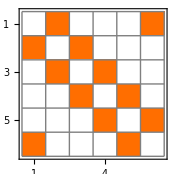

```mathematica
MatrixPlot[myMatrix5, Mesh->True, MeshStyle->Gray]
```

```mathematica
AdjacencyGraph[myMatrix5,DirectedEdges->False,EdgeStyle->Arrowheads[Medium],EdgeShapeFunction->"Arrow" , VertexLabels->"Name",ImagePadding->10]
```

-Graphics-

```mathematica
myMatrix6:=({{0, 1, 1, 1, 1, 1}, {1, 0, 1, 1, 1, 1}, {1, 1, 0, 1, 1, 1}, {1, 1, 1, 0, 1, 1}, {1, 1, 1, 1, 0, 1}, {1, 1, 1, 1, 1, 0}})
```

```mathematica
AdjacencyGraph[myMatrix6,DirectedEdges->False,EdgeStyle->Arrowheads[Medium],EdgeShapeFunction->"Arrow" , VertexLabels->"Name",ImagePadding->10]
```

-Graphics-

```mathematica
myMatrix7:=({{1, 1, 0, 0, 1, 0}, {1, 1, 1, 0, 1, 0}, {0, 1, 0, 1, 0, 0}, {0, 0, 1, 0, 1, 1}, {1, 1, 0, 1, 0, 0}, {0, 0, 0, 1, 0, 0}})
```

```mathematica
AdjacencyGraph[myMatrix7,DirectedEdges->False,EdgeStyle->Arrowheads[Medium],EdgeShapeFunction->"Arrow" , VertexLabels->"Name",ImagePadding->10]
(* Note that nodes (1,1) and (2,2) has value 1. So points back to themselves *)
```

-Graphics-

```mathematica
myMatrixWeek1:=({{0, 1, 0, 0, 1}, {1, 0, 1, 0, 0}, {0, 1, 0, 1, 1}, {0, 0, 1, 0, 1}, {1, 0, 1, 1, 0}})
```

```mathematica
MatrixForm[myMatrixWeek1 . myMatrixWeek1]
```

(2 | 0 | 2 | 1 | 0
0 | 2 | 0 | 1 | 2
2 | 0 | 3 | 1 | 1
1 | 1 | 1 | 2 | 1
0 | 2 | 1 | 1 | 3)

```mathematica
AdjacencyGraph[myMatrixWeek1,DirectedEdges->False,EdgeStyle->Arrowheads[Medium],EdgeShapeFunction->"Arrow", VertexLabels->"Name",ImagePadding->10 ]
```

-Graphics-

```mathematica
GraphDiameter[%1]
```

2

```mathematica
LocalClusteringCoefficient[%1]
```

{0,0,1/3,1,1/3}

```mathematica
GlobalClusteringCoefficient[%1]
```

1/3

```mathematica
myMatrix7:={{0,0,1,0,0,1,0,0},{ 0,0,1,0,0,0,0,0  },{ 1,1,0,1,0,0,0,0},{ 0,0,1,0,1,1,1,0},{ 0,0,0,1,0,0,0,1},{ 1,0,0,1,0,0,0,0},{ 0,0,0,1,0,0,0,1},{ 0,0,0,0,1,0,1,0}}
MatrixForm[myMatrix7]
```

(0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 1 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0)

```mathematica
Diagonal[myMatrix7.Transpose[myMatrix7]]
(* Gets the number of neighbours for all nodes *)
```

{2,1,3,4,2,2,2,2}

```mathematica
AdjacencyGraph[myMatrix7,DirectedEdges->False,VertexLabels->"Name",ImagePadding->10 ]
```

-Graphics-

```mathematica
(* Import Pajek graph files *)
```

```mathematica
myGraph :=Import["C:/coding/Mathematics/Pajek_WorldTrade.net","Elements", magePadding->35]
myGraph
```

{AdjacencyMatrix,EdgeAttributes,EdgeRules,EdgeRulesDirected,Graph,Graphics,VertexAttributes,VertexCount}

```mathematica
myAdjMatrix :=Import["C:/coding/Mathematics/Pajek_WorldTrade.net","AdjacencyMatrix"]
```

```mathematica
AdjacencyGraph[myAdjMatrix,DirectedEdges->False,VertexLabels->"Name",ImagePadding->10 ]
```

-Graphics-

```mathematica
ClosenessCentrality[%2]
```

{0.548611,0.556338,0.589552,0.637097,0.541096,0.530201,0.718182,0.533784,0.544828,0.622047,0.580882,0.576642,0.782178,0.580882,0.544828,0.544828,0.552448,0.572464,0.552448,0.560284,0.548611,0.533784,0.568345,0.77451,0.512987,0.975309,0.560284,0.51634,0.556338,0.552448,0.632,0.564286,0.537415,0.617188,0.556338,0.533784,0.556338,0.918605,0.79,0.560284,0.632,0.533784,0.533784,0.548611,0.568345,0.51634,0.552448,0.560284,0.552448,0.724771,0.560284,0.541096,0.552448,0.530201,0.533784,0.552448,0.533784,0.564286,0.548611,0.556338,0.548611,0.509677,0.519737,0.560284,0.537415,0.598485,0.533784,0.580882,0.686957,0.560284,0.686957,0.647541,0.552448,0.541096,0.556338,0.568345,0.831579,0.918605,0.537415,0.593985}

```mathematica
EigenvectorCentrality[%2]
```

{0.0106043,0.0109718,0.0141157,0.0169902,0.00783465,0.00642052,0.0233602,0.00615181,0.00815985,0.0158593,0.0118985,0.0130134,0.0251024,0.0123499,0.00930679,0.0104127,0.0094113,0.0127422,0.00951562,0.0122278,0.00826194,0.00733717,0.012794,0.0251457,0.00390944,0.0316889,0.0118471,0.00468473,0.00856753,0.00800073,0.0158684,0.0116964,0.00816378,0.0164513,0.0106213,0.0085175,0.0115321,0.0304429,0.026696,0.0119893,0.0182149,0.00843944,0.00716705,0.0109074,0.0118093,0.00468473,0.0112245,0.00845523,0.0115701,0.0241673,0.0117196,0.00628403,0.0108157,0.0075863,0.00847794,0.00775007,0.00697674,0.0109193,0.00962742,0.0113015,0.0106705,0.0033526,0.00498692,0.0101994,0.00740011,0.0148017,0.00740686,0.0145217,0.0213578,0.0118528,0.0220069,0.0189606,0.00946336,0.00813497,0.0116166,0.0132614,0.0286717,0.0305185,0.00825195,0.0138}

```mathematica
DegreeCentrality[%2]
```

{14,16,24,34,12,9,48,11,13,31,22,21,57,22,13,13,15,20,15,17,14,12,19,56,4,77,17,5,16,15,33,18,11,30,16,10,16,72,58,17,33,10,10,14,19,5,15,17,15,49,17,12,15,9,10,15,10,18,14,16,14,5,6,17,11,26,11,22,43,17,43,36,15,12,16,19,63,72,11,25}

```mathematica
(*Social and Economic Networks Week 2 Homework Q1 *)
```

```mathematica
myWeek2Question1graph:={{0,0,0,1,0,0,1},{0,0,0,1,1,0,0},{0,0,0,0,1,0,0},{1,0,0,0,0,0,1},
{0,1,1,0,0,0,0},{0,0,0,0,0,0,1},{1,0,0,1,0,0,0}}
MatrixForm[myWeek2Question1graph]
```

(0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0 | 0 | 0)

```mathematica
AdjacencyGraph[myWeek2Question1graph,DirectedEdges->False,VertexLabels->"Name",ImagePadding->10 ]
```

-Graphics-

```mathematica
ClosenessCentrality[%14] (* Node 4's Closeness Centrality = 3/5 = 0.6) *)
N[6*((2+1+1+1+2+3)^-1)] 
(* Closeness[i] = Formula: Sum[j] * [D<ij>]^-1. j = other nodes. D<ij> = shortest distance between focal node i and other node j *)
(* http://toreopsahl.com/2010/03/20/closeness-centrality-in-networks-with-disconnected-components/ *)
```

{0.461538,0.545455,0.315789,0.6,0.428571,0.352941,0.5}

0.6

```mathematica
DegreeCentrality[%14] (* node 3 and 6 has the smallest Degree Centrality *)
(* = the number of links incident upon a node (i.e.,the number of ties that a node has) *)
```

{2,2,1,3,2,1,3}

```mathematica
BetweennessCentrality[%14] (* TODO: Work out formula! http://en.wikipedia.org/wiki/Centrality#Betweenness_centrality *)
```

{0.,8.,0.,9.,5.,0.,5.}

```mathematica
RandomGraph[{5,6}, VertexLabels->"Name"] (* Generate a random graph on 5 vertices and 6 edges *)
(* http://reference.wolfram.com/mathematica/ref/RandomGraph.html *)
```

-Graphics-

```mathematica
myGraphWeek2Quiz:= {1->2,2->3,1->4,1->5}
g := Graph[myGraphWeek2Quiz,DirectedEdges->False,VertexLabels->"Name",ImagePadding->10 ]
g
```

-Graphics-

```mathematica
ClosenessCentrality[g] (*  Find for node 1: (nodes - 1) * ((1 + 1 + 1 + 2)^(-1))  *)
```

{0.666667,0.8,0.666667,0.666667,0.8}

```mathematica
myGraph:= {"a"->"b","b"->"c","c"->"d","d"->"e","e"->"a","b"->"e"}
g := Graph[myGraph,DirectedEdges->False,VertexLabels->"Name",ImagePadding->2 ]
g
```

-Graphics-

```mathematica
denominator=(Length[VertexList[g]]-1)*(Length[VertexList[g]]-2)/2;
(* Find for node b. NOTE: Denominator = (n-1)(n-2)/2 for undirected graphs. Directed = (n-1)(n-2) *)
ac=1; (* shortest path is a-b-c.Contains b! Contributes 1 *)
ad=0; (* shortest path is a-e-d.Does not contain b. Contributes 0 *)
ae=0; (* length 1. Does not contain b. Contributes 0 *)
cd=0; (* length 1. Does not contain b. Contributes 0 *)
ce=0.5; (* shortest paths are c-d-e and c-b-e. Half of these contain b. So this contributes 0.5 to b's score *)
de=0;  (* length 1. Does not contain b. Contributes 0 *)
(* So b has 1.5 points towards its betweenness centrality. We normalize all scores by dividing by the number of possible pairs we looked at, which was 6 pairs (the pairs do not include b... they were ac,ad,ae,cd,ce,de.) *)
BetweennessCentralityNodeBNormalized=(ac+ad+ae+cd+ce+de)/denominator
BetweennessCentralityNodeB=(ac+ad+ae+cd+ce+de)
bcg = BetweennessCentrality[g]  (* Note: Not normalized! *)
VertexList[g]
(* TIPS: https://class.coursera.org/networksonline-002/forum/thread?thread_id=160 *)
HighlightGraph[g, VertexList[g], VertexSize->Thread[VertexList[g], Rescale[bcg]]]
```

0.25

1.5

{0.,1.5,0.5,0.5,1.5}

{a,b,c,d,e}

-Graphics-